# Dynamical behaviour (version 11-09-2023)

## Classifications of the dynamical behaviour

### Wolfram classes (generic)

```mathematica
(* configuração inicial aleatória *)
Show@GraphicsGrid[Partition[ArrayPlot[CellularAutomaton[#,RandomInteger[{0,1},100],100],PlotLabel->{#,ECADynamics[#,SW]}]&/@{128,172,30,110},2]]
```

-Graphics-

```mathematica
(* configuração inicial...0001000... *)
Show@GraphicsGrid[Partition[ArrayPlot[CellularAutomaton[#,{{1},0},100],PlotLabel->{#,ECADynamics[#,SW]}]&/@{128,172,30,110},2]]
```

-Graphics-

### Li-Packard (specific for ECAs)

```mathematica
(* configuração inicial aleatória *)
Show@GraphicsGrid[Partition[ArrayPlot[CellularAutomaton[#,RandomInteger[{0,1},100],100],PlotLabel->{#,ECADynamics[#,LP]}]&/@{128,72,57,33,134,62,41,110,30},3]]
```

-Graphics-

```mathematica
(* configuração inicial...0001000... *)
Show@GraphicsGrid[Partition[ArrayPlot[CellularAutomaton[#,{{1},0},100],PlotLabel->{#,ECADynamics[#,LP]}]&/@{128,72,57,33,134,62,41,110,30},3]]
```

-Graphics-

### Classification of ECAs with ECADynamics[regra]

```mathematica
ECADynamics[110,SW]
ECADynamics[110,sw]
ECADynamics[110,LP]
ECADynamics[110,lp]
```

Class-IV

CIV

Complex

Cplx

### Question: How many ECAs are there for each “lp” dynamical class, and which are they?

```mathematica
{#,ECADynamics[#,lp]}&/@Range[0,255]
```

{{0,N},{1,P2},{2,Fps},{3,P2s},{4,Fp},{5,P2},{6,P2s},{7,P2s},{8,N},{9,P2s},{10,Fps},{11,P2s},{12,Fp},{13,Fp},{14,P2s},{15,P2s},{16,Fps},{17,P2s},{18,Ch},{19,P2},{20,P2s},{21,P2s},{22,Ch},{23,P2},{24,Fps},{25,P2},{26,Pn},{27,P2s},{28,P2},{29,P2},{30,Ch},{31,P2s},{32,N},{33,P2},{34,Fps},{35,P2s},{36,Fp},{37,P2},{38,P2s},{39,P2s},{40,N},{41,Pn},{42,Fps},{43,P2s},{44,Fp},{45,Ch},{46,Fps},{47,P2s},{48,Fps},{49,P2s},{50,P2},{51,P2},{52,P2s},{53,P2s},{54,Cplx},{55,P2},{56,Fps},{57,Fps},{58,Fps},{59,P2s},{60,Ch},{61,P2},{62,P3},{63,P2s},{64,N},{65,P2s},{66,Fps},{67,P2},{68,Fp},{69,Fp},{70,P2},{71,P2},{72,Fp},{73,Ch},{74,P2s},{75,Ch},{76,Fp},{77,Fp},{78,Fp},{79,Fp},{80,Fps},{81,P2s},{82,Pn},{83,P2s},{84,P2s},{85,P2s},{86,Ch},{87,P2s},{88,P2s},{89,Ch},{90,Ch},{91,P2},{92,Fp},{93,Fp},{94,P3},{95,P2},{96,N},{97,Pn},{98,Fps},{99,Fps},{100,Fp},{101,Ch},{102,Ch},{103,P2},{104,Fp},{105,Ch},{106,Ch},{107,Pn},{108,P2},{109,Ch},{110,Cplx},{111,P2s},{112,Fps},{113,P2s},{114,Fps},{115,P2s},{116,Fps},{117,P2s},{118,P3},{119,P2s},{120,Ch},{121,Pn},{122,Ch},{123,P2},{124,Cplx},{125,P2s},{126,Ch},{127,P2},{128,N},{129,Ch},{130,Fps},{131,P3},{132,Fp},{133,P3},{134,P2s},{135,Ch},{136,N},{137,Cplx},{138,Fps},{139,Fps},{140,Fp},{141,Fp},{142,P2s},{143,P2s},{144,Fps},{145,P3},{146,Ch},{147,Cplx},{148,P2s},{149,Ch},{150,Ch},{151,Ch},{152,Fps},{153,Ch},{154,Pn},{155,P2s},{156,P2},{157,P2},{158,P2s},{159,P2s},{160,N},{161,Ch},{162,Fps},{163,Fps},{164,Fp},{165,Ch},{166,Pn},{167,Pn},{168,N},{169,Ch},{170,Fps},{171,Fps},{172,Fp},{173,P2s},{174,Fps},{175,Fps},{176,Fps},{177,Fps},{178,P2s},{179,P2},{180,Pn},{181,Pn},{182,Ch},{183,Ch},{184,Fps},{185,Fps},{186,Fps},{187,Fps},{188,Fps},{189,Fps},{190,Fps},{191,Fps},{192,N},{193,Cplx},{194,Fps},{195,Ch},{196,Fp},{197,Fp},{198,P2},{199,P2},{200,Fp},{201,P2},{202,Fp},{203,Fp},{204,Fp},{205,Fp},{206,Fp},{207,Fp},{208,Fps},{209,Fps},{210,Pn},{211,P2s},{212,P2s},{213,P2s},{214,P2s},{215,P2s},{216,Fp},{217,Fp},{218,Fp},{219,Fp},{220,Fp},{221,Fp},{222,Fp},{223,Fp},{224,N},{225,Ch},{226,Fps},{227,Fps},{228,Fp},{229,P2s},{230,Fps},{231,Fps},{232,Fp},{233,Fp},{234,N},{235,N},{236,Fp},{237,Fp},{238,N},{239,N},{240,Fps},{241,Fps},{242,Fps},{243,Fps},{244,Fps},{245,Fps},{246,Fps},{247,Fps},{248,N},{249,N},{250,N},{251,N},{252,N},{253,N},{254,N},{255,N}}

```mathematica
GatherBy[Range[0,255],ECADynamics[#,lp]&]//ColumnForm
```

{0,8,32,40,64,96,128,136,160,168,192,224,234,235,238,239,248,249,250,251,252,253,254,255}
{1,5,19,23,25,28,29,33,37,50,51,55,61,67,70,71,91,95,103,108,123,127,156,157,179,198,199,201}
{2,10,16,24,34,42,46,48,56,57,58,66,80,98,99,112,114,116,130,138,139,144,152,162,163,170,171,174,175,176,177,184,185,186,187,188,189,190,191,194,208,209,226,227,230,231,240,241,242,243,244,245,246,247}
{3,6,7,9,11,14,15,17,20,21,27,31,35,38,39,43,47,49,52,53,59,63,65,74,81,83,84,85,87,88,111,113,115,117,119,125,134,142,143,148,155,158,159,173,178,211,212,213,214,215,229}
{4,12,13,36,44,68,69,72,76,77,78,79,92,93,100,104,132,140,141,164,172,196,197,200,202,203,204,205,206,207,216,217,218,219,220,221,222,223,228,232,233,236,237}
{18,22,30,45,60,73,75,86,89,90,101,102,105,106,109,120,122,126,129,135,146,149,150,151,153,161,165,169,182,183,195,225}
{26,41,82,97,107,121,154,166,167,180,181,210}
{54,110,124,137,147,193}
{62,94,118,131,133,145}

```mathematica
ECADynamics[First@#,lp]&/@GatherBy[Range[0,255],ECADynamics[#,lp]&]
```

{N,P2,Fps,P2s,Fp,Ch,Pn,Cplx,P3}

```mathematica
MapThread[
List[#1,#2]&,
{
{"N","P2","Fps","P2s","Fp","Ch","Pn","Cplx","P3"},GatherBy[Range[0,255],ECADynamics[#,lp]&]
}]//ColumnForm
```

{N,{0,8,32,40,64,96,128,136,160,168,192,224,234,235,238,239,248,249,250,251,252,253,254,255}}
{P2,{1,5,19,23,25,28,29,33,37,50,51,55,61,67,70,71,91,95,103,108,123,127,156,157,179,198,199,201}}
{Fps,{2,10,16,24,34,42,46,48,56,57,58,66,80,98,99,112,114,116,130,138,139,144,152,162,163,170,171,174,175,176,177,184,185,186,187,188,189,190,191,194,208,209,226,227,230,231,240,241,242,243,244,245,246,247}}
{P2s,{3,6,7,9,11,14,15,17,20,21,27,31,35,38,39,43,47,49,52,53,59,63,65,74,81,83,84,85,87,88,111,113,115,117,119,125,134,142,143,148,155,158,159,173,178,211,212,213,214,215,229}}
{Fp,{4,12,13,36,44,68,69,72,76,77,78,79,92,93,100,104,132,140,141,164,172,196,197,200,202,203,204,205,206,207,216,217,218,219,220,221,222,223,228,232,233,236,237}}
{Ch,{18,22,30,45,60,73,75,86,89,90,101,102,105,106,109,120,122,126,129,135,146,149,150,151,153,161,165,169,182,183,195,225}}
{Pn,{26,41,82,97,107,121,154,166,167,180,181,210}}
{Cplx,{54,110,124,137,147,193}}
{P3,{62,94,118,131,133,145}}

```mathematica
{First[#],Length[Last[#]]}&/@
MapThread[
List,
{
{"N","P2","Fps","P2s","Fp","Ch","Pn","Cplx","P3"},GatherBy[Range[0,255],ECADynamics[#,lp]&]
}]
```

{{N,24},{P2,28},{Fps,54},{P2s,51},{Fp,43},{Ch,32},{Pn,12},{Cplx,6},{P3,6}}

```mathematica
{#⟦1⟧,Length[#⟦2⟧]}&/@
MapThread[
List,
{
{"N","P2","Fps","P2s","Fp","Ch","Pn","Cplx","P3"},GatherBy[Range[0,255],ECADynamics[#,lp]&]
}]
```

{{N,24},{P2,28},{Fps,54},{P2s,51},{Fp,43},{Ch,32},{Pn,12},{Cplx,6},{P3,6}}

## Classes of Dynamical Equivalence

### Operations of conjugation, reflection, and composition conjugation ◦ reflection (= reflection ◦ conjugation)

#### Idea

#### The operations

Conjugation ( rule 110 ) ⇒ rule 137

Reflection ( rule 110 ) ⇒ rule 124

Conjugation[Reflection[rule 110]]  =  Reflection[Conjugation[rule 110]] ⇒ rule 193

#### Corresponding functions in CAMat.nb

```mathematica
DynamicalEquivalenceClass[110]
DynamicalEquivalenceClass[110,2,1]
```

{{110,2,1},{124,2,1},{137,2,1},{193,2,1}}

{{110,2,1},{124,2,1},{137,2,1},{193,2,1}}

```mathematica
DynamicallyEquivalentRules[110]
DynamicallyEquivalentRules[110,2,1]
```

{{124,2,1},{137,2,1},{193,2,1}}

{{124,2,1},{137,2,1},{193,2,1}}

```mathematica
ConjugateRules[110,2,1]
ReflectedRule[110,2,1]
ConjugateReflectedRules[110,2,1]
ReflectedConjugateRules[110]
```

{{137,2,1}}

{124,2,1}

{{193,2,1}}

{{193,2,1}}

#### Table from the NKS book, p. 883 (which corresponds to page 899 in the PDF)

#### Rules with asymmetrical neighbourhood (1/2, 3/2, etc...)

```mathematica
DynamicalEquivalenceClass[{#,2,0.5}]&/@Range[0,15]//MatrixForm
```

({{0,2,0.5},{15,2,0.5}}
{{1,2,0.5},{7,2,0.5}}
{{2,2,0.5},{11,2,0.5}}
{{3,2,0.5}}
{{4,2,0.5},{13,2,0.5}}
{{5,2,0.5}}
{{6,2,0.5},{9,2,0.5}}
{{1,2,0.5},{7,2,0.5}}
{{8,2,0.5},{14,2,0.5}}
{{6,2,0.5},{9,2,0.5}}
{{10,2,0.5}}
{{2,2,0.5},{11,2,0.5}}
{{12,2,0.5}}
{{4,2,0.5},{13,2,0.5}}
{{8,2,0.5},{14,2,0.5}}
{{0,2,0.5},{15,2,0.5}})

```mathematica
Union[SortBy[%,First]]//MatrixForm
```

({{3,2,0.5}}
{{5,2,0.5}}
{{10,2,0.5}}
{{12,2,0.5}}
{{0,2,0.5},{15,2,0.5}}
{{1,2,0.5},{7,2,0.5}}
{{2,2,0.5},{11,2,0.5}}
{{4,2,0.5},{13,2,0.5}}
{{6,2,0.5},{9,2,0.5}}
{{8,2,0.5},{14,2,0.5}})

```mathematica
ConjugateRules[{#,2,0.5}]&/@Range[0,15]//Column
```

{{15,2,0.5}}
{{7,2,0.5}}
{{11,2,0.5}}
{{3,2,0.5}}
{{13,2,0.5}}
{{5,2,0.5}}
{{9,2,0.5}}
{{1,2,0.5}}
{{14,2,0.5}}
{{6,2,0.5}}
{{10,2,0.5}}
{{2,2,0.5}}
{{12,2,0.5}}
{{4,2,0.5}}
{{8,2,0.5}}
{{0,2,0.5}}

```mathematica
ReflectedRule[{#,2,0.5}]&/@Range[0,15]//Column
```

{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}

### Periodic boundary condition: initial configuration 0...0001 for all rules

```mathematica
Print@GraphicsRow[ArrayPlot[CellularAutomaton[#,Join[Table[0,{50}],{1}],50],PlotLabel->#]&/@{110,137,124,193}]
```

-Graphics-

### Periodic boundary condition: initial configuration 0...0001 and the three operations on it

```mathematica
Join[Table[0,{50}],{1}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
1-Join[Table[0,{50}],{1}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0}

```mathematica
Reverse@Join[Table[0,{50}],{1}]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
1-Reverse@Join[Table[0,{50}],{1}]
```

{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Print@GraphicsRow@MapThread[ArrayPlot[CellularAutomaton[#1,#2,55],PlotLabel->#1]&,{{110,137,124,193},
{Join[Table[0,{50}],{1}],
1-Join[Table[0,{50}],{1}],
Reverse@Join[Table[0,{50}],{1}],
1-Reverse@Join[Table[0,{50}],{1}]}}]
```

-Graphics-

```mathematica
ECADynamics[#,sw]&/@{110,137,124,193}
ECADynamics[#,lp]&/@{110,137,124,193}
```

{CIV,CIV,CIV,CIV}

{Cplx,Cplx,Cplx,Cplx}

```mathematica
ECADynamics[#,sw]&/@First@DynamicalEquivalenceClass[30]
ECADynamics[#,lp]&/@First@DynamicalEquivalenceClass[30]
```

{CIII,CII,CII}

{Ch,Fps,P2}

```mathematica
DynamicalEquivalenceClass[205]
ECADynamics[#,sw]&/@First@DynamicalEquivalenceClass[205]
ECADynamics[#,lp]&/@First@DynamicalEquivalenceClass[205]
```

{{76,2,1},{205,2,1}}

{CII,CII,CII}

{Fp,Fps,P2}

### Non-periodic boundary condition (fixed, null): initial configuration ...0001000...

```mathematica
Print@GraphicsRow[ArrayPlot[CellularAutomaton[#,{{1},0},55],PlotLabel->#]&/@{110,137,124,193}]
```

-Graphics-

### Non-periodic boundary condition (fixed, null): initial configuration ...0001000... and the operations on it

```mathematica
Print@GraphicsRow@MapThread[ArrayPlot[CellularAutomaton[#1,#2,55],PlotLabel->#1]&,{{110,137,124,193},
{{{1},0},
{{0},1},
{{1},0},
{{0},1}}}]
```

-Graphics-

### Generalisation for k > 2

```mathematica
RuleTable[45676547,3,1]/.{0->White,1->Black,2->Red}
```

{{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},GrayLevel[1]},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[0]},GrayLevel[1]},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1]},GrayLevel[1]},{{RGBColor[1, 0, 0],GrayLevel[0],RGBColor[1, 0, 0]},GrayLevel[1]},{{RGBColor[1, 0, 0],GrayLevel[0],GrayLevel[0]},GrayLevel[1]},{{RGBColor[1, 0, 0],GrayLevel[0],GrayLevel[1]},GrayLevel[1]},{{RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0]},GrayLevel[1]},{{RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[0]},GrayLevel[1]},{{RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1]},GrayLevel[1]},{{GrayLevel[0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},GrayLevel[1]},{{GrayLevel[0],RGBColor[1, 0, 0],GrayLevel[0]},GrayLevel[0]},{{GrayLevel[0],RGBColor[1, 0, 0],GrayLevel[1]},GrayLevel[1]},{{GrayLevel[0],GrayLevel[0],RGBColor[1, 0, 0]},GrayLevel[1]},{{GrayLevel[0],GrayLevel[0],GrayLevel[0]},GrayLevel[0]},{{GrayLevel[0],GrayLevel[0],GrayLevel[1]},GrayLevel[0]},{{GrayLevel[0],GrayLevel[1],RGBColor[1, 0, 0]},RGBColor[1, 0, 0]},{{GrayLevel[0],GrayLevel[1],GrayLevel[0]},RGBColor[1, 0, 0]},{{GrayLevel[0],GrayLevel[1],GrayLevel[1]},GrayLevel[0]},{{GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},GrayLevel[0]},{{GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[0]},RGBColor[1, 0, 0]},{{GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1]},GrayLevel[0]},{{GrayLevel[1],GrayLevel[0],RGBColor[1, 0, 0]},GrayLevel[0]},{{GrayLevel[1],GrayLevel[0],GrayLevel[0]},GrayLevel[1]},{{GrayLevel[1],GrayLevel[0],GrayLevel[1]},RGBColor[1, 0, 0]},{{GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0]},RGBColor[1, 0, 0]},{{GrayLevel[1],GrayLevel[1],GrayLevel[0]},RGBColor[1, 0, 0]},{{GrayLevel[1],GrayLevel[1],GrayLevel[1]},RGBColor[1, 0, 0]}}

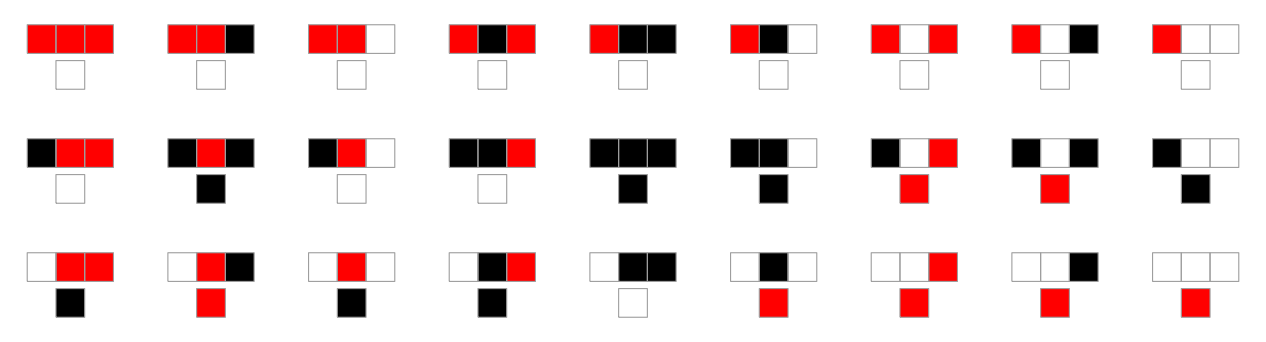

```mathematica
RulePlot[CellularAutomaton[{45676547,3,1}],ColorRules->{0->White,1->Black,2->Red}]
```

```mathematica
Permutations[{White,Black,Red}]
```

{{GrayLevel[1],GrayLevel[0],RGBColor[1, 0, 0]},{GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[0]},{GrayLevel[0],GrayLevel[1],RGBColor[1, 0, 0]},{GrayLevel[0],RGBColor[1, 0, 0],GrayLevel[1]},{RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[0]},{RGBColor[1, 0, 0],GrayLevel[0],GrayLevel[1]}}

```mathematica
{{0->0,1->1,2->2},{0->0,1->2,2->1},{0->1,1->0,2->2},{0->1,1->2,2->0},{0->2,1->0,2->1},{0->2,1->1,2->0}}/.{0->White,1->Black,2->Red}//Column
```

{GrayLevel[1]→GrayLevel[1],GrayLevel[0]→GrayLevel[0],RGBColor[1, 0, 0]→RGBColor[1, 0, 0]}
{GrayLevel[1]→GrayLevel[1],GrayLevel[0]→RGBColor[1, 0, 0],RGBColor[1, 0, 0]→GrayLevel[0]}
{GrayLevel[1]→GrayLevel[0],GrayLevel[0]→GrayLevel[1],RGBColor[1, 0, 0]→RGBColor[1, 0, 0]}
{GrayLevel[1]→GrayLevel[0],GrayLevel[0]→RGBColor[1, 0, 0],RGBColor[1, 0, 0]→GrayLevel[1]}
{GrayLevel[1]→RGBColor[1, 0, 0],GrayLevel[0]→GrayLevel[1],RGBColor[1, 0, 0]→GrayLevel[0]}
{GrayLevel[1]→RGBColor[1, 0, 0],GrayLevel[0]→GrayLevel[0],RGBColor[1, 0, 0]→GrayLevel[1]}

```mathematica
ConjugateRules[45676547,3,1]
ReflectedRule[45676547,3,1]
ConjugateReflectedRules[45676547,3,1]
DynamicalEquivalenceClass[45676547,3,1]
%//Length
```

{{77233730039,3,1},{3686693357211,3,1},{3812647694607,3,1},{5842300979695,3,1},{7132181787283,3,1}}

{296062750787,3,1}

{{1471076618039,3,1},{3006147341487,3,1},{4326171183771,3,1},{5286382543855,3,1},{6231554198323,3,1}}

{{45676547,3,1},{77233730039,3,1},{296062750787,3,1},{1471076618039,3,1},{3006147341487,3,1},{3686693357211,3,1},{3812647694607,3,1},{4326171183771,3,1},{5286382543855,3,1},{5842300979695,3,1},{6231554198323,3,1},{7132181787283,3,1}}

12

### 2 Questions

#### Question 1: How many dynamically equivalent classes are there in the elementary space, and which are they?

```mathematica
DynamicalEquivalenceClass[110]
DynamicalEquivalenceClass[137]
```

{{110,2,1},{124,2,1},{137,2,1},{193,2,1}}

{{110,2,1},{124,2,1},{137,2,1},{193,2,1}}

```mathematica
equivalenceECAClasses=GatherBy[Range[0,255],DynamicalEquivalenceClass[#]&]
%//Length
First/@%%
```

{{0,255},{1,127},{2,16,191,247},{3,17,63,119},{4,223},{5,95},{6,20,159,215},{7,21,31,87},{8,64,239,253},{9,65,111,125},{10,80,175,245},{11,47,81,117},{12,68,207,221},{13,69,79,93},{14,84,143,213},{15,85},{18,183},{19,55},{22,151},{23},{24,66,189,231},{25,61,67,103},{26,82,167,181},{27,39,53,83},{28,70,157,199},{29,71},{30,86,135,149},{32,251},{33,123},{34,48,187,243},{35,49,59,115},{36,219},{37,91},{38,52,155,211},{40,96,235,249},{41,97,107,121},{42,112,171,241},{43,113},{44,100,203,217},{45,75,89,101},{46,116,139,209},{50,179},{51},{54,147},{56,98,185,227},{57,99},{58,114,163,177},{60,102,153,195},{62,118,131,145},{72,237},{73,109},{74,88,173,229},{76,205},{77},{78,92,141,197},{90,165},{94,133},{104,233},{105},{106,120,169,225},{108,201},{110,124,137,193},{122,161},{126,129},{128,254},{130,144,190,246},{132,222},{134,148,158,214},{136,192,238,252},{138,174,208,244},{140,196,206,220},{142,212},{146,182},{150},{152,188,194,230},{154,166,180,210},{156,198},{160,250},{162,176,186,242},{164,218},{168,224,234,248},{170,240},{172,202,216,228},{178},{184,226},{200,236},{204},{232}}

88

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,18,19,22,23,24,25,26,27,28,29,30,32,33,34,35,36,37,38,40,41,42,43,44,45,46,50,51,54,56,57,58,60,62,72,73,74,76,77,78,90,94,104,105,106,108,110,122,126,128,130,132,134,136,138,140,142,146,150,152,154,156,160,162,164,168,170,172,178,184,200,204,232}

#### Question 2: Which are the possible sizes of the dynamically equivalent classes of the elementary space, and how frequently do they occur?

```mathematica
Length/@equivalenceECAClasses
Union[%]
```

{2,2,4,4,2,2,4,4,4,4,4,4,4,4,4,2,2,2,2,1,4,4,4,4,4,2,4,2,2,4,4,2,2,4,4,4,4,2,4,4,4,2,1,2,4,2,4,4,4,2,2,4,2,1,4,2,2,2,1,4,2,4,2,2,2,4,2,4,4,4,4,2,2,1,4,4,2,2,4,2,4,2,4,1,2,2,1,1}

{1,2,4}

```mathematica
Select[equivalenceECAClasses,(Length[#]==1)&]
%//Length
```

{{23},{51},{77},{105},{150},{178},{204},{232}}

8

```mathematica
Select[equivalenceECAClasses,(Length[#]==2)&]
%//Length
```

{{0,255},{1,127},{4,223},{5,95},{15,85},{18,183},{19,55},{22,151},{29,71},{32,251},{33,123},{36,219},{37,91},{43,113},{50,179},{54,147},{57,99},{72,237},{73,109},{76,205},{90,165},{94,133},{104,233},{108,201},{122,161},{126,129},{128,254},{132,222},{142,212},{146,182},{156,198},{160,250},{164,218},{170,240},{184,226},{200,236}}

36

```mathematica
Select[equivalenceECAClasses,(Length[#]==4)&]
%//Length
```

{{2,16,191,247},{3,17,63,119},{6,20,159,215},{7,21,31,87},{8,64,239,253},{9,65,111,125},{10,80,175,245},{11,47,81,117},{12,68,207,221},{13,69,79,93},{14,84,143,213},{24,66,189,231},{25,61,67,103},{26,82,167,181},{27,39,53,83},{28,70,157,199},{30,86,135,149},{34,48,187,243},{35,49,59,115},{38,52,155,211},{40,96,235,249},{41,97,107,121},{42,112,171,241},{44,100,203,217},{45,75,89,101},{46,116,139,209},{56,98,185,227},{58,114,163,177},{60,102,153,195},{62,118,131,145},{74,88,173,229},{78,92,141,197},{106,120,169,225},{110,124,137,193},{130,144,190,246},{134,148,158,214},{136,192,238,252},{138,174,208,244},{140,196,206,220},{152,188,194,230},{154,166,180,210},{162,176,186,242},{168,224,234,248},{172,202,216,228}}

44

## Degrees of internal symmetry

### Definition

Example:
											    -Graphics-

```mathematica
CountSymmetry[110,2,1,{stBWTransform}]
CountSymmetry[110,2,1,{stLRTransform}]
CountSymmetry[110,2,1,{stBWLRTransform}]
CountSymmetry[110,2,1,{stLRBWTransform}]
```

{2}

{6}

{2}

{2}

```mathematica
CountSymmetry[110,2,1,{stBWTransform,stLRTransform,stBWLRTransform}]
```

{2,6,2}

```mathematica
CountSymmetry[#,2,1,{stBWTransform,stLRTransform,stBWLRTransform}]&/@{110,137,124,193}
```

{{2,6,2},{2,6,2},{2,6,2},{2,6,2}}

### 4 Questions

#### Question 1: Let’s define a pattern of internal symmetry degree as the symmetry counts ordered as {BW, LR, BWLR}. Which are the possible patterns of internal symmetry degree in the elementary space, and how many are they?

```mathematica
CountSymmetry[#, 2, 1, {stBWTransform, stLRTransform, stBWLRTransform}]&/@(First/@equivalenceECAClasses)
```

{{0,8,0},{2,8,2},{2,6,2},{4,6,4},{2,8,2},{4,8,4},{4,6,4},{6,6,6},{2,6,2},{4,6,4},{4,4,0},{6,4,2},{4,6,4},{6,6,6},{6,4,2},{8,4,4},{4,8,4},{6,8,6},{6,8,6},{8,8,8},{0,4,4},{2,4,6},{2,6,2},{4,6,4},{2,4,6},{4,4,8},{4,6,4},{2,8,2},{4,8,4},{4,6,4},{6,6,6},{0,8,0},{2,8,2},{2,6,2},{4,6,4},{6,6,6},{6,4,2},{8,4,4},{2,6,2},{4,6,4},{4,4,0},{6,8,6},{8,8,8},{4,8,4},{2,4,6},{4,4,8},{4,6,4},{0,4,4},{2,6,2},{4,8,4},{6,8,6},{2,6,2},{6,8,6},{8,8,8},{4,6,4},{0,8,0},{2,8,2},{6,8,6},{8,8,8},{4,6,4},{4,8,4},{2,6,2},{2,8,2},{0,8,0},{2,8,2},{4,6,4},{4,8,4},{6,6,6},{4,6,4},{6,4,2},{6,6,6},{8,4,4},{6,8,6},{8,8,8},{2,4,6},{4,6,4},{4,4,8},{4,8,4},{6,6,6},{2,8,2},{6,6,6},{8,4,4},{4,6,4},{8,8,8},{4,4,8},{6,8,6},{8,8,8},{8,8,8}}

```mathematica
Union[%]
```

{{0,4,4},{0,8,0},{2,4,6},{2,6,2},{2,8,2},{4,4,0},{4,4,8},{4,6,4},{4,8,4},{6,4,2},{6,6,6},{6,8,6},{8,4,4},{8,8,8}}

```mathematica
Union[CountSymmetry[#, 2, 1, {stBWTransform, stLRTransform, stBWLRTransform}]&/@Range[0,255]]
```

{{0,4,4},{0,8,0},{2,4,6},{2,6,2},{2,8,2},{4,4,0},{4,4,8},{4,6,4},{4,8,4},{6,4,2},{6,6,6},{6,8,6},{8,4,4},{8,8,8}}

```mathematica
%//Length
```

14

#### Question 2: How frequent are the patterns of internal symmetry degree in the elementary space?

```mathematica
SortBy[Tally[CountSymmetry[#, 2, 1, {stBWTransform,stLRTransform,stBWLRTransform}]&/@Range[0,255]],Last]
Total[Last/@%]
```

{{{0,4,4},8},{{0,8,0},8},{{4,4,0},8},{{4,4,8},8},{{8,4,4},8},{{8,8,8},8},{{2,4,6},16},{{2,8,2},16},{{4,8,4},16},{{6,4,2},16},{{6,8,6},16},{{2,6,2},32},{{6,6,6},32},{{4,6,4},64}}

256

```mathematica
SortBy[Tally[CountSymmetry[#,2,1,{stBWTransform,stLRTransform,stBWLRTransform}]&/@(First/@equivalenceECAClasses)],Last]
Total[Last/@%]
```

{{{0,4,4},2},{{4,4,0},2},{{0,8,0},4},{{2,4,6},4},{{4,4,8},4},{{6,4,2},4},{{8,4,4},4},{{2,6,2},8},{{2,8,2},8},{{4,8,4},8},{{6,6,6},8},{{6,8,6},8},{{8,8,8},8},{{4,6,4},16}}

88

#### Question 3: How are the patterns of internal symmetry degree associated to the representatives of each dynamical class of the elementary space?

```mathematica
Module[{symPattern=#},
{symPattern,Select[First/@equivalenceECAClasses,(CountSymmetry[#,2,1,{stBWTransform,stLRTransform,stBWLRTransform}]==symPattern)&]}]&/@{{0,4,4},{0,8,0},{2,4,6},{2,6,2},{2,8,2},{4,4,0},{4,4,8},{4,6,4},{4,8,4},{6,4,2},{6,6,6},{6,8,6},{8,4,4},{8,8,8}}//Column
```

{{0,4,4},{24,60}}
{{0,8,0},{0,36,90,126}}
{{2,4,6},{25,28,56,152}}
{{2,6,2},{2,8,26,38,44,62,74,110}}
{{2,8,2},{1,4,32,37,94,122,128,164}}
{{4,4,0},{10,46}}
{{4,4,8},{29,57,156,184}}
{{4,6,4},{3,6,9,12,27,30,34,40,45,58,78,106,130,136,154,172}}
{{4,8,4},{5,18,33,54,72,108,132,160}}
{{6,4,2},{11,14,42,138}}
{{6,6,6},{7,13,35,41,134,140,162,168}}
{{6,8,6},{19,22,50,73,76,104,146,200}}
{{8,4,4},{15,43,142,170}}
{{8,8,8},{23,51,77,105,150,178,204,232}}

#### Question 4: Is there a clear correlation between the patterns of internal symmetry and the sizes of the dynamical equivalence classes of the elementary space?

```mathematica
{Length@DynamicalEquivalenceClass[#],CountSymmetry[#,2,1,{stBWTransform,stLRTransform,stBWLRTransform}]}&/@(First/@equivalenceECAClasses)
Union[%]
GatherBy[%,First[#]&]//Column
```

{{2,{0,8,0}},{2,{2,8,2}},{4,{2,6,2}},{4,{4,6,4}},{2,{2,8,2}},{2,{4,8,4}},{4,{4,6,4}},{4,{6,6,6}},{4,{2,6,2}},{4,{4,6,4}},{4,{4,4,0}},{4,{6,4,2}},{4,{4,6,4}},{4,{6,6,6}},{4,{6,4,2}},{2,{8,4,4}},{2,{4,8,4}},{2,{6,8,6}},{2,{6,8,6}},{1,{8,8,8}},{4,{0,4,4}},{4,{2,4,6}},{4,{2,6,2}},{4,{4,6,4}},{4,{2,4,6}},{2,{4,4,8}},{4,{4,6,4}},{2,{2,8,2}},{2,{4,8,4}},{4,{4,6,4}},{4,{6,6,6}},{2,{0,8,0}},{2,{2,8,2}},{4,{2,6,2}},{4,{4,6,4}},{4,{6,6,6}},{4,{6,4,2}},{2,{8,4,4}},{4,{2,6,2}},{4,{4,6,4}},{4,{4,4,0}},{2,{6,8,6}},{1,{8,8,8}},{2,{4,8,4}},{4,{2,4,6}},{2,{4,4,8}},{4,{4,6,4}},{4,{0,4,4}},{4,{2,6,2}},{2,{4,8,4}},{2,{6,8,6}},{4,{2,6,2}},{2,{6,8,6}},{1,{8,8,8}},{4,{4,6,4}},{2,{0,8,0}},{2,{2,8,2}},{2,{6,8,6}},{1,{8,8,8}},{4,{4,6,4}},{2,{4,8,4}},{4,{2,6,2}},{2,{2,8,2}},{2,{0,8,0}},{2,{2,8,2}},{4,{4,6,4}},{2,{4,8,4}},{4,{6,6,6}},{4,{4,6,4}},{4,{6,4,2}},{4,{6,6,6}},{2,{8,4,4}},{2,{6,8,6}},{1,{8,8,8}},{4,{2,4,6}},{4,{4,6,4}},{2,{4,4,8}},{2,{4,8,4}},{4,{6,6,6}},{2,{2,8,2}},{4,{6,6,6}},{2,{8,4,4}},{4,{4,6,4}},{1,{8,8,8}},{2,{4,4,8}},{2,{6,8,6}},{1,{8,8,8}},{1,{8,8,8}}}

{{1,{8,8,8}},{2,{0,8,0}},{2,{2,8,2}},{2,{4,4,8}},{2,{4,8,4}},{2,{6,8,6}},{2,{8,4,4}},{4,{0,4,4}},{4,{2,4,6}},{4,{2,6,2}},{4,{4,4,0}},{4,{4,6,4}},{4,{6,4,2}},{4,{6,6,6}}}

{{1,{8,8,8}}}
{{2,{0,8,0}},{2,{2,8,2}},{2,{4,4,8}},{2,{4,8,4}},{2,{6,8,6}},{2,{8,4,4}}}
{{4,{0,4,4}},{4,{2,4,6}},{4,{2,6,2}},{4,{4,4,0}},{4,{4,6,4}},{4,{6,4,2}},{4,{6,6,6}}}

Conclusion: 
— Classes of dynamical equivalence with 1 rule: {8, 8, 8}; 
— Classes of dynamical equivalence with 2 rules: {4, 4, 8}, {8, 4, 4} or {x, 8, x}, with x ∈ {0, 2, 4, 6}; and
— Classes of dynamical equivalence with 4 rules: {0, 4, 4}, {4, 4, 0}, {2, 4, 6}, {6, 4, 2} or {x, 6, x}, with x ∈ {2, 4, 6}.

#### Note: Colour blind rules are those with maximal internal symmetry due to conjugation

```mathematica
Union[CountSymmetry[#,2,1,{stBWTransform,stLRTransform,stBWLRTransform}]&/@Select[Range[0,255],ColourBlindRuleQ[#]&]]
```

{{8,4,4},{8,8,8}}

```mathematica
Union[CountSymmetry[#,2,1,{stBWTransform,stLRTransform,stBWLRTransform}]&/@Select[Range[0,255],¬ColourBlindRuleQ[#]&]]
```

{{0,4,4},{0,8,0},{2,4,6},{2,6,2},{2,8,2},{4,4,0},{4,4,8},{4,6,4},{4,8,4},{6,4,2},{6,6,6},{6,8,6}}

```mathematica
Length[Join[%,%%]]
```

14